```mathematica
CL=ClojureEvaluate
```

ClojureEvaluate

```mathematica
import[quote[org․apache․hadoop․hbase․util․Bytes]]//ClojureEvaluate
```

«JavaObject[java.lang.Class]»

```mathematica
SetClojureLinkAutoReplacements[EvaluationNotebook[]]
```

```mathematica
mideasters={"oshaokhtmeligi","Lujee","norashalaby","TwiddleEastNews","pressfreedom","ghazalairshad","NouralAdly","drnemovet","Angela_Deane","GayMiddleEast","Advox","demotix","iyad_elbaghdadi","netraKL","ElNa7aS_Pasha","hfakhry","TEDataEgypt","themoornextdoor","hebalsherif","ElBaradei","Mohamed_Bary","amrwaked","MarcusMonopoli","TauxFu","tamsinchan","CaireneGirl","ZeroSilence","Gemyhood","BooDy","Ghafari","ANaje","ahmedsamih","oke1985","salmaeldaly","MAswad","BikyaMasr","Ramikantari","AmmarMa","DidiRemez","sarahussein","jricole","Warchadi","asteris","ghoshworld","DanRaviv","freearab","Crowdmap","CrisisMappers","occupiedcairo","anjucomet","AbdullaBnS","M_ElMotasem","EngyG","brericsson","LeilaFadel","krmaher","ashrafkhalil","JaredCohen","BloggerSeif","jpalfrey","daliamosaad","democracynow","LobnaAkrab","BDUTT","monamahfouz","eskandarany","aayatun","alfagih","ahmada2","waelabbas","nevin_A","remon_z","hmlc","Amiralx","BBCGavinLee","nadinetoukan","habibh","Sarahngb","etharkamal","Ali_Bahnasawy","lrozen","matthewteller","RamyYaacoub","hadeelalsh","qubadjt","prashantrao","NadiaE","Ssirgany","FromJoanne","estr4ng3d","ellozy","gr33ndata","WANA_FORUM","Gsquare86","ianinegypt","anthonyshadid","Lastoadri","jilliancyork","BaghdadBrian","gharbeia","ziad_mohi","Mozn","jstacher","monasosh","Sandmonkey","farazrabbani","omarc","daliaziada","habibahamid","haaretzonline","harrietsherwood","MennaGamal","TravellerW","Sarahcarr","AmrEzzat","sarahspeakstome","shadysamir","maggieosama","tabulagaza","moftasa","Zeinobia","Raafatology","beleidy","khadijapatel","azadessa","mmbilal","nashwanasreldin","mbaa","mohamed","hamish6PM","ragehomaar","omarkhalifa","mrayyan","safdar","moeed","Riy","EnoughGaddafi","FreeLibya","Cyrenaican","AymanM","Brian_Whit","HooverInst","haaretzopinion","camanpour","Jerusalem_Post","joshmull","kv64info","ahramEgypt","BrookingsInst","hrw","witnessorg","BrookingsFP","CFR_org","USIP","CrisisGroup","AliveInEgypt","evanchill","JacksonDiehl","alaa","Ghonim","stevenacook","joshrogin","MJayRosenberg","georgehale","justimage","borzou","ryandevereaux","Linaattalah","naveenaqvi","hackneylad","Omar_Gaza","jeremyscahill","3arabawy","sharifkouddous","mathieubastian","RamyRaoof","Elshaheeed","SherineT","yasmineryan","abdu","htgamal","afinighan","Desert_Dals","fpleitgenCNN","mosharrafzaidi","NickKristof","jrug","piyachatto","NaheedMustafa","Londonstani","bungdan","khalidalkhalifa","emile_hokayem","AJCountingCost","AlMasryAlYoum_E","SudaneseThinker","ahmed","lassecgen","bbclysedoucet","margaortigas","FTMiddleEast","manal","SaeedCNN","jonjensen","avilewis","melissakchan","RawyaRageh","AlanFisher","Moadow","glcarlstrom","Dima_Khatib","AJRizKhan","newgyptian","IvanCNN","phijazin","alexhanna","monaeltahawy","TrellaLB","blakehounshell","bencnn","bsebti","nolanjazeera","jordantimes","Nabeelrajab","gamaleid","shadihamid","Max_Fisher","FP_Magazine","BabakDehghan","Almezel","RaviCNN","HalaGorani","ArabRevolution","moalkhalifa","MiddleEastInst","tweetsintheME","RobAtState","sarahmckoolking","emilydparker","onwardcaro","erin_pelton","eliselabottcnn","PJCrowley","AlecJRoss","Katulis","abumuqawama","abuaardvark","AmjadAtallah","arabist","mwhanna1","WSJMidEast","SultanAlQassemi","AJELive","AJEnglish"};
```

## clojure-twitter

```mathematica
use[quote[clojure․contrib․json]]//CL
```

```mathematica
require[quote[twitter]]//CL
```

```mathematica
require[quote[{oauth․client,։as,oauth}]]//CL
```

```mathematica
def[oauth‑consumer,oauth`make‑consumer["gf6hR6WixpxWRoTPzLSh3w","YiOJQZmwZCKyXjEsPiRsgLxINER7mPSUbA55AZNAIko","https://api.twitter.com/oauth/request_token","https://api.twitter.com/oauth/access_token","https://api.twitter.com/oauth/authorize",։hmac‑sha1]]//CL
```

«JavaObject[clojure.lang.Var]»

```mathematica
def[oauth‑access‑token,"2933441-J2x9hoG54wd3VVIUDz4rJsQroYaTa6CQQGfSFr5tAS"]//CL
```

«JavaObject[clojure.lang.Var]»

```mathematica
def[oauth‑access‑token‑secret,"S8eMWaqqeUengEajY49mZU7V2QMrcSy4wdF5SHObg"]//CL
```

«JavaObject[clojure.lang.Var]»

### nowmov_mideast token

```mathematica
def[oauth‑access‑token,"248478681-LpeQtGrghK3TXo8A2kWm6XB3MWtUvowGRIVG1Yj0"]//CL
```

«JavaObject[clojure.lang.Var]»

```mathematica
def[oauth‑access‑token‑secret,"PWtOIOFpqqlFRh913DBTcEQG8YJBDRc8iUipkIgfE"]//CL
```

«JavaObject[clojure.lang.Var]»

### userinfo

```mathematica
twitter`with‑oauth[oauth‑consumer, oauth‑access‑token,oauth‑access‑token‑secret,twitter`lookup‑users‑by‑id[ "16529829"]]//CL
```

{{։status→{։text→Profiled some of my code in latest guile and it is cooking with gas! Looking forward to pending 2.0 release.,։retweetˍcount→0,։coordinates→Null,։inˍreplyˍtoˍstatusˍidˍstr→Null,։contributors→Null,։inˍreplyˍtoˍuserˍidˍstr→Null,։idˍstr→33670065526145025,։inˍreplyˍtoˍscreenˍname→Null,։retweeted→False,։truncated→False,։createdˍat→Fri Feb 04 23:35:43 +0000 2011,։geo→Null,։place→Null,։inˍreplyˍtoˍstatusˍid→Null,։favorited→False,։source→<a href="http://itunes.apple.com/app/twitter/id333903271?mt=8" rel="nofollow">Twitter for iPad</a>,։id→33670065526145025,։inˍreplyˍtoˍuserˍid→Null},։profileˍuseˍbackgroundˍimage→False,։followˍrequestˍsent→False,։profileˍsidebarˍfillˍcolor→ffffff,։protected→False,։following→False,։profileˍbackgroundˍimageˍurl→http://a2.twimg.com/profile_background_images/187232855/reddit.jpg,։contributorsˍenabled→False,։favouritesˍcount→0,։timeˍzone→London,։name→zedstar@freenode,։idˍstr→16529829,։listedˍcount→1,։utcˍoffset→0,։profileˍlinkˍcolor→3a2f82,։profileˍbackgroundˍtile→True,։location→London,։statusesˍcount→2690,։followersˍcount→111,։friendsˍcount→251,։createdˍat→Tue Sep 30 16:21:00 +0000 2008,։lang→en,։profileˍsidebarˍborderˍcolor→00103d,։url→http://zedstar.org,։notifications→False,։profileˍbackgroundˍcolor→ffffff,։geoˍenabled→False,։showˍallˍinlineˍmedia→False,։isˍtranslator→False,։profileˍimageˍurl→http://a2.twimg.com/profile_images/1202646646/me_normal.jpg,։verified→False,։id→16529829,։description→FSF #6831,։profileˍtextˍcolor→080808,։screenˍname→jptmoore}}

## timeline->hbase

### into hbase

```mathematica
sampleTimeline[username_]:=CL[(let[{tweetlist,twitter`with‑oauth[oauth‑consumer, oauth‑access‑token,oauth‑access‑token‑secret,twitter`user‑timeline[։id, username,։count,"200"]]},map[fn[{tweet},hb`with‑table[{t,hb`table["tweets"]},hb`put[t,str[։screenˍname[։user[tweet]],"/",։idˍstr[tweet]],։values,{։raw,{։json,json‑str[tweet]}}]]],tweetlist]])]
```

```mathematica
mideasters[[3]]
```

norashalaby

```mathematica
(Print[#];sampleTimeline[#])&/@Drop[mideasters,3];
```

### out of hbase

```mathematica
hb`with‑table[{test‑tbl,hb`table["tweets"]},
hb`with‑scanner[{scan‑results,hb`scan[test‑tbl,։start‑row,"Lujee"]},map[fn[{yy},read‑json[last@first@get‑in[hb`as‑map[yy,։map‑value,fn[{x},Bytes`toString[x]],։map‑family,fn[{x},Bytes`toString[x]],։map‑qualifier,fn[{x},Bytes`toString[x]]],{"raw","json"}]]],doall@seq@scan‑results]]
]//CL
```

```mathematica
hb`with‑table[{test‑tbl,hb`table["tweets"]},
hb`with‑scanner[{scan‑results,hb`scan[test‑tbl,։start‑row,"Lujee"]},map[fn[{yy},read‑json[last@first@get‑in[hb`as‑map[yy,։map‑value->fn[{x},Bytes`toString[x]],։map‑family->fn[{x},Bytes`toString[x]],։map‑qualifier->fn[{x},Bytes`toString[x]]],{"raw","json"}]]],doall@seq@scan‑results]]
]//CL
```

### get specific user’s tweets

```mathematica
hb`with‑table[{test‑tbl,hb`table["tweets"]},
hb`with‑scanner[{scan‑results,hb`scan[test‑tbl,։start‑row,"Lujee",։stop‑row,"Lujee1"]},count@seq@scan‑results]
]//CL
```

981

```mathematica
UserTweets[uname_]:=hb`with‑table[{test‑tbl,hb`table["tweets"]},
hb`with‑scanner[{scan‑results,hb`scan[test‑tbl,։start‑row,uname,։stop‑row,uname<>"1"]},map[fn[{yy},read‑json[last@first@get‑in[hb`as‑map[yy,։map‑value->fn[{x},Bytes`toString[x]],։map‑family->fn[{x},Bytes`toString[x]],։map‑qualifier->fn[{x},Bytes`toString[x]]],{"raw","json"}]]],doall@seq@scan‑results]]
]//CL
```

```mathematica
arabicfraction=#->With[{s=Flatten@ToCharacterCode@((։text/.#)&/@UserTweets[#])},N[Length@Select[s,#>1000&]/Length[s]]]&/@mideasters
```

{oshaokhtmeligi→0.692446,Lujee→0.0120522,norashalaby→0.00387886,TwiddleEastNews→0.000507292,pressfreedom→0.00102655,ghazalairshad→0.,NouralAdly→0.000582581,drnemovet→0.652693,Angela_Deane→0.000516987,GayMiddleEast→0.00448016,Advox→0.000991988,demotix→0.0000491497,iyad_elbaghdadi→0.0173707,netraKL→0.000907441,ElNa7aS_Pasha→0.650544,hfakhry→Indeterminate,TEDataEgypt→0.0483895,themoornextdoor→0.0213035,hebalsherif→0.0310083,ElBaradei→0.463147,Mohamed_Bary→0.017495,amrwaked→0.399279,MarcusMonopoli→0.,TauxFu→0.000069541,tamsinchan→0.000102838,CaireneGirl→0.00999737,ZeroSilence→0.,Gemyhood→0.65853,BooDy→0.59693,Ghafari→0.269906,ANaje→0.724473,ahmedsamih→0.637125,oke1985→0.578713,salmaeldaly→0.257178,MAswad→0.214642,BikyaMasr→0.00304085,Ramikantari→0.00115255,AmmarMa→0.031745,DidiRemez→0.00133382,sarahussein→0.005306,jricole→0.00368815,Warchadi→0.0170026,asteris→0.,ghoshworld→0.,DanRaviv→0.,freearab→0.0107222,Crowdmap→0.0000880592,CrisisMappers→0.000991753,occupiedcairo→0.00278983,anjucomet→0.000252602,AbdullaBnS→0.330507,M_ElMotasem→0.412026,EngyG→0.205066,brericsson→0.000425849,LeilaFadel→0.000714669,krmaher→0.00172882,ashrafkhalil→0.,JaredCohen→0.,BloggerSeif→0.000131874,jpalfrey→0.000338203,daliamosaad→0.231005,democracynow→0.00122419,LobnaAkrab→0.131373,BDUTT→0.,monamahfouz→0.227084,eskandarany→0.677796,aayatun→Indeterminate,alfagih→0.629478,ahmada2→0.458854,waelabbas→0.522705,nevin_A→0.529283,remon_z→0.0300412,hmlc→0.806306,Amiralx→0.0096175,BBCGavinLee→Indeterminate,nadinetoukan→0.0262635,habibh→0.00014771,Sarahngb→0.0612138,etharkamal→0.110802,Ali_Bahnasawy→0.0127225,lrozen→0.000435161,matthewteller→0.00214133,RamyYaacoub→0.0146797,hadeelalsh→0.,qubadjt→0.00411829,prashantrao→0.,NadiaE→0.13301,Ssirgany→0.094171,FromJoanne→0.000506073,estr4ng3d→0.0493373,ellozy→0.137544,gr33ndata→0.291372,WANA_FORUM→0.0048905,Gsquare86→0.,ianinegypt→0.,anthonyshadid→0.000144907,Lastoadri→0.412707,jilliancyork→0.00478386,BaghdadBrian→0.000281246,gharbeia→0.154695,ziad_mohi→0.118734,Mozn→0.0956143,jstacher→0.000320595,monasosh→0.0275035,Sandmonkey→0.00765585,farazrabbani→0.00446615,omarc→0.000190682,daliaziada→0.206645,habibahamid→0.000745156,haaretzonline→0.0000560099,harrietsherwood→0.,MennaGamal→0.0285532,TravellerW→0.0172861,Sarahcarr→0.024593,AmrEzzat→0.644935,sarahspeakstome→0.112199,shadysamir→0.145779,maggieosama→0.300999,tabulagaza→0.0686152,moftasa→0.111689,Zeinobia→0.000995733,Raafatology→0.0965564,beleidy→0.00833711,khadijapatel→0.000172068,azadessa→0.000187441,mmbilal→0.000117089,nashwanasreldin→0.000174825,mbaa→0.346702,mohamed→0.000160832,hamish6PM→0.,ragehomaar→0.,omarkhalifa→0.00202135,mrayyan→0.0358979,safdar→0.00129796,moeed→0.000686813,Riy→0.000133209,EnoughGaddafi→0.0191558,FreeLibya→0.0453649,Cyrenaican→0.00190665,AymanM→0.0043345,Brian_Whit→0.000395765,HooverInst→0.00177548,haaretzopinion→0.000311526,camanpour→0.00330989,Jerusalem_Post→0.00106614,joshmull→0.000536513,kv64info→0.000118255,ahramEgypt→0.00948466,BrookingsInst→0.0000454814,hrw→0.00111458,witnessorg→0.000609942,BrookingsFP→0.000132223,CFR_org→0.000851271,USIP→0.000738314,CrisisGroup→0.0140823,AliveInEgypt→0.00721342,evanchill→0.000049838,JacksonDiehl→0.,alaa→0.174804,Ghonim→0.129939,stevenacook→0.,joshrogin→0.00111612,MJayRosenberg→0.,georgehale→0.00384731,justimage→0.0028208,borzou→0.00111143,ryandevereaux→0.000272777,Linaattalah→0.0278412,naveenaqvi→0.000268543,hackneylad→0.0000485201,Omar_Gaza→0.,jeremyscahill→0.000319387,3arabawy→0.194764,sharifkouddous→0.000197922,mathieubastian→0.000248917,RamyRaoof→0.128459,Elshaheeed→0.643184,SherineT→0.000514815,yasmineryan→0.0000899038,abdu→0.00553264,htgamal→0.0044287,afinighan→0.,Desert_Dals→0.000160884,fpleitgenCNN→0.,mosharrafzaidi→0.000191013,NickKristof→0.,jrug→0.0000517786,piyachatto→0.,NaheedMustafa→0.000756501,Londonstani→0.00755005,bungdan→0.,khalidalkhalifa→0.0645892,emile_hokayem→0.000190449,AJCountingCost→0.,AlMasryAlYoum_E→0.000620312,SudaneseThinker→0.00427422,ahmed→0.0285714,lassecgen→0.804709,bbclysedoucet→0.,margaortigas→0.,FTMiddleEast→0.00271862,manal→0.0904312,SaeedCNN→0.000571184,jonjensen→0.,avilewis→0.,melissakchan→0.00466211,RawyaRageh→0.00038289,AlanFisher→0.000341734,Moadow→0.,glcarlstrom→0.0000430126,Dima_Khatib→0.277261,AJRizKhan→0.00139346,newgyptian→0.00939828,IvanCNN→0.000136624,phijazin→0.174147,alexhanna→0.00186335,monaeltahawy→0.,TrellaLB→0.197477,blakehounshell→0.000123138,bencnn→0.000214915,bsebti→0.0133279,nolanjazeera→0.,jordantimes→0.00446224,Nabeelrajab→0.276058,gamaleid→0.672939,shadihamid→0.,Max_Fisher→0.00023371,FP_Magazine→0.00171939,BabakDehghan→0.,Almezel→0.0554947,RaviCNN→0.,HalaGorani→0.000161091,ArabRevolution→0.0016888,moalkhalifa→0.00360821,MiddleEastInst→0.000195491,tweetsintheME→0.,RobAtState→0.000959437,sarahmckoolking→0.000226381,emilydparker→0.00612813,onwardcaro→0.000378621,erin_pelton→0.00023988,eliselabottcnn→0.000420676,PJCrowley→0.0000797925,AlecJRoss→0.0668991,Katulis→0.00451128,abumuqawama→0.000205787,abuaardvark→0.000178851,AmjadAtallah→0.00030567,arabist→0.00842072,mwhanna1→0.,WSJMidEast→0.,SultanAlQassemi→0.000399645,AJELive→0.,AJEnglish→0.}

```mathematica
SortBy[%,Last]
```

{afinighan→0.,AJCountingCost→0.,AJELive→0.,AJEnglish→0.,ashrafkhalil→0.,asteris→0.,avilewis→0.,BabakDehghan→0.,bbclysedoucet→0.,BDUTT→0.,bungdan→0.,DanRaviv→0.,fpleitgenCNN→0.,ghazalairshad→0.,ghoshworld→0.,Gsquare86→0.,hadeelalsh→0.,hamish6PM→0.,harrietsherwood→0.,ianinegypt→0.,JacksonDiehl→0.,JaredCohen→0.,jonjensen→0.,MarcusMonopoli→0.,margaortigas→0.,MJayRosenberg→0.,Moadow→0.,monaeltahawy→0.,mwhanna1→0.,NickKristof→0.,nolanjazeera→0.,Omar_Gaza→0.,piyachatto→0.,prashantrao→0.,ragehomaar→0.,RaviCNN→0.,shadihamid→0.,stevenacook→0.,tweetsintheME→0.,WSJMidEast→0.,ZeroSilence→0.,glcarlstrom→0.0000430126,BrookingsInst→0.0000454814,hackneylad→0.0000485201,demotix→0.0000491497,evanchill→0.000049838,jrug→0.0000517786,haaretzonline→0.0000560099,TauxFu→0.000069541,PJCrowley→0.0000797925,Crowdmap→0.0000880592,yasmineryan→0.0000899038,tamsinchan→0.000102838,mmbilal→0.000117089,kv64info→0.000118255,blakehounshell→0.000123138,BloggerSeif→0.000131874,BrookingsFP→0.000132223,Riy→0.000133209,IvanCNN→0.000136624,anthonyshadid→0.000144907,habibh→0.00014771,mohamed→0.000160832,Desert_Dals→0.000160884,HalaGorani→0.000161091,khadijapatel→0.000172068,nashwanasreldin→0.000174825,abuaardvark→0.000178851,azadessa→0.000187441,emile_hokayem→0.000190449,omarc→0.000190682,mosharrafzaidi→0.000191013,MiddleEastInst→0.000195491,sharifkouddous→0.000197922,abumuqawama→0.000205787,bencnn→0.000214915,sarahmckoolking→0.000226381,Max_Fisher→0.00023371,erin_pelton→0.00023988,mathieubastian→0.000248917,anjucomet→0.000252602,naveenaqvi→0.000268543,ryandevereaux→0.000272777,BaghdadBrian→0.000281246,AmjadAtallah→0.00030567,haaretzopinion→0.000311526,jeremyscahill→0.000319387,jstacher→0.000320595,jpalfrey→0.000338203,AlanFisher→0.000341734,onwardcaro→0.000378621,RawyaRageh→0.00038289,Brian_Whit→0.000395765,SultanAlQassemi→0.000399645,eliselabottcnn→0.000420676,brericsson→0.000425849,lrozen→0.000435161,FromJoanne→0.000506073,TwiddleEastNews→0.000507292,SherineT→0.000514815,Angela_Deane→0.000516987,joshmull→0.000536513,SaeedCNN→0.000571184,NouralAdly→0.000582581,witnessorg→0.000609942,AlMasryAlYoum_E→0.000620312,moeed→0.000686813,LeilaFadel→0.000714669,USIP→0.000738314,habibahamid→0.000745156,NaheedMustafa→0.000756501,CFR_org→0.000851271,netraKL→0.000907441,RobAtState→0.000959437,CrisisMappers→0.000991753,Advox→0.000991988,Zeinobia→0.000995733,pressfreedom→0.00102655,Jerusalem_Post→0.00106614,borzou→0.00111143,hrw→0.00111458,joshrogin→0.00111612,Ramikantari→0.00115255,democracynow→0.00122419,safdar→0.00129796,DidiRemez→0.00133382,AJRizKhan→0.00139346,ArabRevolution→0.0016888,FP_Magazine→0.00171939,krmaher→0.00172882,HooverInst→0.00177548,alexhanna→0.00186335,Cyrenaican→0.00190665,omarkhalifa→0.00202135,matthewteller→0.00214133,FTMiddleEast→0.00271862,occupiedcairo→0.00278983,justimage→0.0028208,BikyaMasr→0.00304085,camanpour→0.00330989,moalkhalifa→0.00360821,jricole→0.00368815,georgehale→0.00384731,norashalaby→0.00387886,qubadjt→0.00411829,SudaneseThinker→0.00427422,AymanM→0.0043345,htgamal→0.0044287,jordantimes→0.00446224,farazrabbani→0.00446615,GayMiddleEast→0.00448016,Katulis→0.00451128,melissakchan→0.00466211,jilliancyork→0.00478386,WANA_FORUM→0.0048905,sarahussein→0.005306,abdu→0.00553264,emilydparker→0.00612813,AliveInEgypt→0.00721342,Londonstani→0.00755005,Sandmonkey→0.00765585,beleidy→0.00833711,arabist→0.00842072,newgyptian→0.00939828,ahramEgypt→0.00948466,Amiralx→0.0096175,CaireneGirl→0.00999737,freearab→0.0107222,Lujee→0.0120522,Ali_Bahnasawy→0.0127225,bsebti→0.0133279,CrisisGroup→0.0140823,RamyYaacoub→0.0146797,Warchadi→0.0170026,TravellerW→0.0172861,iyad_elbaghdadi→0.0173707,Mohamed_Bary→0.017495,EnoughGaddafi→0.0191558,themoornextdoor→0.0213035,Sarahcarr→0.024593,nadinetoukan→0.0262635,monasosh→0.0275035,Linaattalah→0.0278412,MennaGamal→0.0285532,ahmed→0.0285714,remon_z→0.0300412,hebalsherif→0.0310083,AmmarMa→0.031745,mrayyan→0.0358979,FreeLibya→0.0453649,TEDataEgypt→0.0483895,estr4ng3d→0.0493373,Almezel→0.0554947,Sarahngb→0.0612138,khalidalkhalifa→0.0645892,AlecJRoss→0.0668991,tabulagaza→0.0686152,manal→0.0904312,Ssirgany→0.094171,Mozn→0.0956143,Raafatology→0.0965564,etharkamal→0.110802,moftasa→0.111689,sarahspeakstome→0.112199,ziad_mohi→0.118734,RamyRaoof→0.128459,Ghonim→0.129939,LobnaAkrab→0.131373,NadiaE→0.13301,ellozy→0.137544,shadysamir→0.145779,gharbeia→0.154695,phijazin→0.174147,alaa→0.174804,3arabawy→0.194764,TrellaLB→0.197477,EngyG→0.205066,daliaziada→0.206645,MAswad→0.214642,monamahfouz→0.227084,daliamosaad→0.231005,salmaeldaly→0.257178,Ghafari→0.269906,Nabeelrajab→0.276058,Dima_Khatib→0.277261,gr33ndata→0.291372,maggieosama→0.300999,AbdullaBnS→0.330507,mbaa→0.346702,amrwaked→0.399279,M_ElMotasem→0.412026,Lastoadri→0.412707,ahmada2→0.458854,ElBaradei→0.463147,waelabbas→0.522705,nevin_A→0.529283,oke1985→0.578713,BooDy→0.59693,alfagih→0.629478,ahmedsamih→0.637125,Elshaheeed→0.643184,AmrEzzat→0.644935,ElNa7aS_Pasha→0.650544,drnemovet→0.652693,Gemyhood→0.65853,gamaleid→0.672939,eskandarany→0.677796,oshaokhtmeligi→0.692446,ANaje→0.724473,lassecgen→0.804709,hmlc→0.806306,aayatun→Indeterminate,BBCGavinLee→Indeterminate,hfakhry→Indeterminate}

### iteratively populate tweets

```mathematica
CL[(let[{tweetlist,twitter`with‑oauth[oauth‑consumer, oauth‑access‑token,oauth‑access‑token‑secret,twitter`user‑timeline[։id, "Lujee",։page,"9",։count,"200"]]},count[tweetlist]])]
```

$Failed

```mathematica
DateList["Tue Feb 08 20:14:12"]
```

{2011,2,8,20,14,12.}

if last date is before the min date, stop

```mathematica
AsMap[]
```

```mathematica
GetIn[]
```

[:id
   :user-id
   :screen-name
   :since-id
   :max-id
   :count
   :page]

use paging??

## follow user

## friends

```mathematica
Grid[{։screenˍname,։description}/.#[[2,1]]&/@friendprofiles,Frame->All]
```

```mathematica
Position[։screenˍname/.#[[2,1]]&/@Take[friendprofiles,259],"AJEnglish"]
```

{{259}}

```mathematica
CL[(hb`with‑table[{t,hb`table["users"]},hb`put[t,։screenˍname/.#[[2,1]],։values,{։profile,{։json,json‑str[#[[2,1]]]}}]])]&/@Take[friendprofiles,259]
```

```mathematica
friendprofiles=Take[friendprofiles,259];
```

```mathematica
friendprofiles=Delete[friendprofiles,3]
```

```mathematica
Flatten[(։screenˍname/.#)&/@Last/@friendprofiles]
```

```mathematica
Length[{"oshaokhtmeligi","Lujee","norashalaby","TwiddleEastNews","pressfreedom","ghazalairshad","NouralAdly","drnemovet","Angela_Deane","GayMiddleEast","Advox","demotix","iyad_elbaghdadi","netraKL","ElNa7aS_Pasha","hfakhry","TEDataEgypt","themoornextdoor","hebalsherif","ElBaradei","Mohamed_Bary","amrwaked","MarcusMonopoli","TauxFu","tamsinchan","CaireneGirl","ZeroSilence","Gemyhood","BooDy","Ghafari","ANaje","ahmedsamih","oke1985","salmaeldaly","MAswad","BikyaMasr","Ramikantari","AmmarMa","DidiRemez","sarahussein","jricole","Warchadi","asteris","ghoshworld","DanRaviv","freearab","Crowdmap","CrisisMappers","occupiedcairo","anjucomet","AbdullaBnS","M_ElMotasem","EngyG","brericsson","LeilaFadel","krmaher","ashrafkhalil","JaredCohen","BloggerSeif","jpalfrey","daliamosaad","democracynow","LobnaAkrab","BDUTT","monamahfouz","eskandarany","aayatun","alfagih","ahmada2","waelabbas","nevin_A","remon_z","hmlc","Amiralx","BBCGavinLee","nadinetoukan","habibh","Sarahngb","etharkamal","Ali_Bahnasawy","lrozen","matthewteller","RamyYaacoub","hadeelalsh","qubadjt","prashantrao","NadiaE","Ssirgany","FromJoanne","estr4ng3d","ellozy","gr33ndata","WANA_FORUM","Gsquare86","ianinegypt","anthonyshadid","Lastoadri","jilliancyork","BaghdadBrian","gharbeia","ziad_mohi","Mozn","jstacher","monasosh","Sandmonkey","farazrabbani","omarc","daliaziada","habibahamid","haaretzonline","harrietsherwood","MennaGamal","TravellerW","Sarahcarr","AmrEzzat","sarahspeakstome","shadysamir","maggieosama","tabulagaza","moftasa","Zeinobia","Raafatology","beleidy","khadijapatel","azadessa","mmbilal","nashwanasreldin","mbaa","mohamed","hamish6PM","ragehomaar","omarkhalifa","mrayyan","safdar","moeed","Riy","EnoughGaddafi","FreeLibya","Cyrenaican","AymanM","Brian_Whit","HooverInst","haaretzopinion","camanpour","Jerusalem_Post","joshmull","kv64info","ahramEgypt","BrookingsInst","hrw","witnessorg","BrookingsFP","CFR_org","USIP","CrisisGroup","AliveInEgypt","evanchill","JacksonDiehl","alaa","Ghonim","stevenacook","joshrogin","MJayRosenberg","georgehale","justimage","borzou","ryandevereaux","Linaattalah","naveenaqvi","hackneylad","Omar_Gaza","jeremyscahill","3arabawy","sharifkouddous","mathieubastian","RamyRaoof","Elshaheeed","SherineT","yasmineryan","abdu","htgamal","afinighan","Desert_Dals","fpleitgenCNN","mosharrafzaidi","NickKristof","jrug","piyachatto","NaheedMustafa","Londonstani","bungdan","khalidalkhalifa","emile_hokayem","AJCountingCost","AlMasryAlYoum_E","SudaneseThinker","ahmed","lassecgen","bbclysedoucet","margaortigas","FTMiddleEast","manal","SaeedCNN","jonjensen","avilewis","melissakchan","RawyaRageh","AlanFisher","Moadow","glcarlstrom","Dima_Khatib","AJRizKhan","newgyptian","IvanCNN","phijazin","alexhanna","monaeltahawy","TrellaLB","blakehounshell","bencnn","bsebti","nolanjazeera","jordantimes","Nabeelrajab","gamaleid","shadihamid","Max_Fisher","FP_Magazine","BabakDehghan","Almezel","RaviCNN","HalaGorani","ArabRevolution","moalkhalifa","MiddleEastInst","tweetsintheME","RobAtState","sarahmckoolking","emilydparker","onwardcaro","erin_pelton","eliselabottcnn","PJCrowley","AlecJRoss","Katulis","abumuqawama","abuaardvark","AmjadAtallah","arabist","mwhanna1","WSJMidEast","SultanAlQassemi","AJELive","AJEnglish"}]
```

254

## profile

```mathematica
ImportProfile[screenname_]:=oauth[let[{u,twitter`show‑user‑by‑name[screenname]},SetProfile[screenname,u],u]]
```

```mathematica
SetProfile[name_,profile_]:=hb`with‑table[{t,hb`table["users"]},hb`put[t,name,։values,{։profile,{։json,json‑str[profile]}}]]
```

```mathematica
GetProfile[screenname_]:=(hb`with‑table[{t,hb`table["users"]},read‑json@last@first@get‑in[hb`as‑map[hb`get[t,screenname,։columns,{։cf1}],։map‑value,fn[{x},Bytes`toString[x]],։map‑family,fn[{x},Bytes`toString[x]],։map‑qualifier,fn[{x},Bytes`toString[x]]],{"profile","json"}]])
```

```mathematica
CL@ImportProfile[#]&/@mideasters;
```

```mathematica
CL@twitter`show‑user‑by‑name["sarahmckoolking"]
```

{։status→{։text→@fojolbros thanks for some awesome butter chicken today.  You should park near @StateDept more often!,։retweetˍcount→0,։coordinates→Null,։inˍreplyˍtoˍstatusˍidˍstr→Null,։contributors→Null,։inˍreplyˍtoˍuserˍidˍstr→30913789,։idˍstr→35117618222465024,։inˍreplyˍtoˍscreenˍname→fojolbros,։retweeted→False,։truncated→False,։createdˍat→Tue Feb 08 23:27:47 +0000 2011,։geo→Null,։place→Null,։inˍreplyˍtoˍstatusˍid→Null,։favorited→False,։source→web,։id→35117618222465024,։inˍreplyˍtoˍuserˍid→30913789},։profileˍuseˍbackgroundˍimage→True,։followˍrequestˍsent→False,։profileˍsidebarˍfillˍcolor→E3E2DE,։protected→False,։following→False,։profileˍbackgroundˍimageˍurl→http://a2.twimg.com/profile_background_images/83916146/Washington_twitter_2.jpg,։contributorsˍenabled→False,։favouritesˍcount→0,։timeˍzone→Eastern Time (US & Canada),։name→Sarah King,։idˍstr→111627089,։listedˍcount→37,։utcˍoffset→-18000,։profileˍlinkˍcolor→088253,։profileˍbackgroundˍtile→True,։location→Washington, DC,։statusesˍcount→548,։followersˍcount→564,։friendsˍcount→295,։createdˍat→Fri Feb 05 16:00:30 +0000 2010,։lang→en,։profileˍsidebarˍborderˍcolor→D3D2CF,։url→Null,։notifications→False,։profileˍbackgroundˍcolor→EDECE9,։geoˍenabled→True,։showˍallˍinlineˍmedia→False,։isˍtranslator→False,։profileˍimageˍurl→http://a0.twimg.com/profile_images/683395411/OAS_foto_normal.jpg,։verified→False,։id→111627089,։description→Foreign Policy wonk-ette, Washington enthusiast, Californian at heart,։profileˍtextˍcolor→634047,։screenˍname→sarahmckoolking}

```mathematica
uidmapping=Cases[Rule@@@(CL@let[{u,GetProfile[#]},{#,։id[u]}]&/@mideasters),_Rule];
```

## jan25 friends

```mathematica
oauth[x_]:=twitter`with‑oauth[oauth‑consumer, oauth‑access‑token,oauth‑access‑token‑secret,x]
```

```mathematica
ImportFriendsIDs[name_]:=oauth[let[{ids,twitter`friends‑of‑name[name]},SetFriendsIDs[name,ids],ids]]
```

```mathematica
SetFriendsIDs[name_,followers_]:=hb`with‑table[{t,hb`table["users"]},hb`put[t,name,։values,{։graph,{։friendids,json‑str[followers]}}]]
```

```mathematica
CL@ImportFriendsIDs["TwiddleEastNews"]
```

```mathematica
ImportFollowerIDs["oshaokhtmeligi"]//CL
```

```mathematica
CL@twitter`with‑oauth[oauth‑consumer,oauth‑access‑token,oauth‑access‑token‑secret,hb`with‑table[{t,hb`table["users"]},hb`put[t,"oshaokhtmeligi",։values,{։graph,{։friendids,json‑str[twitter`friends‑of‑name["oshaokhtmeligi"]]}}]]]
```

```mathematica
GetFriendsIDs[name_]:=read‑json@last@first@get‑in[hb`with‑table[{t,hb`table["users"]},hb`as‑map[hb`get[t,name,։columns,{։graph,{։friendids} }],։map‑value,fn[{x},Bytes`toString[x]],։map‑family,fn[{x},Bytes`toString[x]],։map‑qualifier,fn[{x},Bytes`toString[x]]]],{"graph","friendids"}]
```

```mathematica
CL@ImportFollowerIDs[#]&/@mideasters;
```

```mathematica
((#/.uidmapping)->Select[CL@GetFriendsIDs[#],keepQ])&/@mideasters
```

```mathematica
arabicfraction2=arabicfraction/.uidmapping;
```

```mathematica
arabicfraction[[1]]
```

oshaokhtmeligi→0.692446

```mathematica
<<GraphUtilitie
```

```mathematica
graph=Graph@Union[Sort/@Intersection[Union@Flatten[Thread/@%266],Reverse/@Union@Flatten[Thread/@%266]]];
```

```mathematica
dropvertices=First/@Select[Transpose[{VertexList[graph],VertexDegree[graph]}],Last[#]===1&];
```

```mathematica
Select[Union[Sort/@Intersection[Union@Flatten[Thread/@%266],Reverse/@Union@Flatten[Thread/@%266]]],FreeQ[#,Alternatives@@dropvertices]&]
```

```mathematica
Export["/mideast3.graphml",%305/.(Reverse/@uidmapping)]
```

/mideast3.graphml

```mathematica
GraphPlot[%%%]
```

```mathematica
graph2=VertexDelete[graph,First/@Select[Transpose[{VertexList[graph],VertexDegree[graph]}],Last[#]===1&]];
```

{163014260,9739482,19489239,14973978,15432218,17001490,16466545,135476005,23925541,18725815,69181624,19083676,19681513,49728986,23572083,27414710,25071839,36615385,52511395,151106990,202557701}

```mathematica
VertexDegree[graph]
```

{16,35,43,34,47,29,19,31,32,32,29,41,4,32,24,66,3,16,21,33,9,67,38,18,10,19,14,38,29,22,25,21,17,11,20,19,19,25,32,24,26,4,12,18,23,8,39,74,27,17,20,48,50,13,31,24,36,34,32,12,45,38,32,9,29,20,30,19,22,22,19,24,33,36,9,20,3,24,21,5,30,24,48,15,24,19,7,12,13,16,37,21,36,16,13,4,41,15,17,26,36,15,4,3,3,18,21,13,19,23,10,7,14,13,10,18,17,12,16,12,9,20,13,4,19,7,4,10,16,20,4,8,11,11,15,10,8,10,9,4,37,14,9,15,7,1,12,12,2,4,7,3,11,1,7,7,17,10,13,10,22,6,19,7,12,7,4,2,1,3,6,7,4,5,2,17,5,5,8,6,3,4,1,2,1,6,4,7,10,9,1,2,1,10,7,1,7,2,6,3,4,2,2,4,3,7,1,5,1,1,1,5,3,2,2,1,4,1,1,1,3,3,1,1,1,5,3,1,2,1}

```mathematica
Count[%289,2]
```

11

```mathematica
Count[%,1]
```

21

```mathematica
Options[GraphPlot]
```

{AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DirectedEdges→False,DisplayFunction:>$DisplayFunction,EdgeLabeling→True,EdgeRenderingFunction→Automatic,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→None,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Method→Automatic,MultiedgeStyle→Automatic,PackingMethod→Automatic,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,SelfLoopStyle→Automatic,Ticks→Automatic,TicksStyle→{},VertexCoordinateRules→Automatic,VertexLabeling→Automatic,VertexRenderingFunction→Automatic}

```mathematica
GraphPlot[First@graph2,VertexRenderingFunction->({Blend[{Blue,Green},2*(#2/.arabicfraction2)/. Except[_Real]->0],Point[#1]}&),DirectedEdges->False]
```

$Aborted[]

```mathematica
Normal@graph2
```

```mathematica
Length[graph2]
```

0

```mathematica
mideastgraph1=CL@With[{name=(։screenˍname/.#[[2,1]])},let[{user,hb`with‑table[{t,hb`table["users"]},hb`as‑map[hb`get[t,name,։columns,{։graph ->։friendids}],։map‑value,fn[{x},Bytes`toString[x]],։map‑family,fn[{x},Bytes`toString[x]],։map‑qualifier,fn[{x},Bytes`toString[x]]]]},
{
let[{x,read‑json@last@first@get‑in[user,{"profile","json"}]},{։id@x,։screenˍname@x}],
read‑json[last@first@get‑in[user,{"graph","friendids"}]]}
]]&/@friendprofiles;
```

```mathematica
uidmapping=Rule@@@(CL@let[{u,GetProfile[#]},{#,։id[u]}]&/@mideasters);
```

```mathematica
(keepQ[#]=True)&/@Last/@uidmapping;
```

```mathematica
Last/@uidmapping
```

```mathematica
??keepQ
```

Global`keepQ

```mathematica
mideastgraph2=#[[1,1]]->Select[Last[#],keepQ]&/@mideastgraph1;
```

```mathematica
mideastgraph2[[10]]
```

```mathematica
18650093->{18833257,1924421,92546663,4970411,106840674,18429664,23079148,138787319,83590349,9576102,82282572,1921671,5242,69181624,85243004,29979814,14048901,2168011,9378802,9739482,20867867,16935292,1285451,17004618,14700316}
```

{5242→302683,5242→1921671,5242→2168011,5242→3419141,5242→5108161,5242→6090052,5242→7489012,5242→8787362,5242→9201822,5242→12599812,5242→15196372,5242→17774777,5242→18267544,5242→23188724,5242→24136198,5242→52998468,«3440»,238845761→11316572,238845761→18011386,238845761→24264540,238845761→29979814,238845761→238843898,239152755→608583,239152755→9201822,239152755→14048901,239152755→18011386,239152755→29979814,239152755→158067539,239152755→159827281,242718658→3419141,242718658→18480789,242718658→20301135,242718658→23926671}

```mathematica
Length[Intersection[Reverse/@Flatten[Thread/@mideastgraph2],Flatten[Thread/@mideastgraph2]]]
```

3472

```mathematica
Length[Reverse/@Flatten[Thread/@mideastgraph2]]
```

7396

5242→1921671

```mathematica
?Export
```

Export[file.ext,expr] exports data to a file, converting it to the format corresponding to the file extension ext. 
Export[file,expr,format] exports data in the specified format.
Export[file,exprs,elems] exports data by treating exprs as elements specified by elems.

```mathematica
?GXL
```

```mathematica
Union[Sort/@Intersection[Reverse/@Flatten[Thread/@mideastgraph2],Flatten[Thread/@mideastgraph2]]]
```

```mathematica
Export["/mideast.graphml",Union[Sort/@Intersection[Reverse/@Flatten[Thread/@mideastgraph2],Flatten[Thread/@mideastgraph2]]],"graphml"]
```

/mideast.graphml

```mathematica
Graph@Union[Sort/@Intersection[Reverse/@Flatten[Thread/@mideastgraph2],Flatten[Thread/@mideastgraph2]]]
```

```mathematica
VertexList[Union[Sort/@Intersection[Reverse/@Flatten[Thread/@mideastgraph2],Flatten[Thread/@mideastgraph2]]]]//Length
```

1

```mathematica
?Graph
```

Graph[{e_1,e_2,…}] yields a graph with edges e_j.
Graph[{v_1,v_2,…},{{e_1,e_2,…}] yields the graph with vertices v_i and edges e_j. 
Graph[{…,w_i[v_i,…],…},{…,w_j[e_j,…],…}] yields a graph with vertex and edge properties defined by the symbolic wrappers w_k.

```mathematica
Import["~/mideast2.graphml"]
```

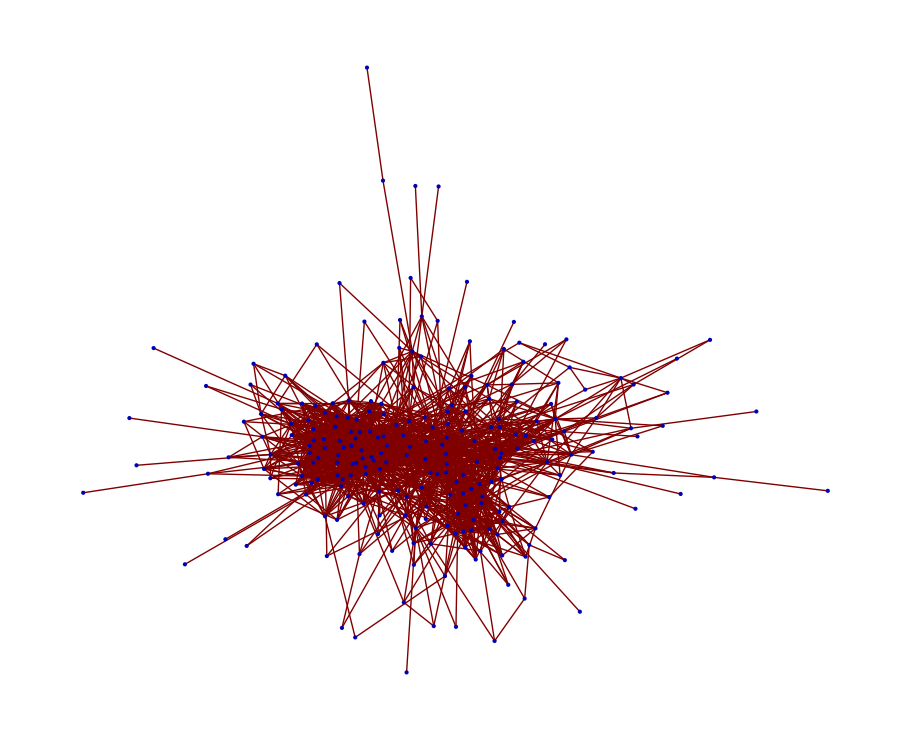

```mathematica
GraphPlot[Union[Sort/@Intersection[Reverse/@Flatten[Thread/@mideastgraph2],Flatten[Thread/@mideastgraph2]]],SelfLoopStyle->None]
```

```mathematica
mideastgraph2
```

{14619728→{},65375759→{},7067102→{},14375609→{},1285451→{},31576969→{},21589783→{},78417474→{},2696831→{},18650093→{},25529018→{},247301389→{},43937371→{},15336943→{},56727397→{},9739482→{},15067830→{},18725815→{},36615385→{},88714870→{},48094796→{},101734884→{},18728732→{},127825476→{},119360445→{},202557701→{},230288829→{},49680877→{},215844036→{},61211686→{},39059828→{},182745161→{},3655491→{},2204711→{},5872932→{},8787362→{},40701142→{},11562822→{},202872841→{},17017496→{},74446328→{},14126888→{},45567561→{},90184020→{},108668795→{},17001490→{},25058400→{},9378802→{},244957467→{},19083676→{},243811449→{},142388142→{},106840674→{},18307147→{},30029450→{},49728986→{},27414710→{},37264417→{},18197610→{},80077721→{},16434823→{},61440064→{},33039483→{},159827281→{},21097230→{},190261453→{},16935292→{},242718658→{},19929890→{},18480789→{},15863493→{},24481693→{},52998468→{},12745892→{},2168011→{},14315883→{},23925541→{},14442420→{},42597278→{},18632368→{},28991368→{},20719191→{},20301135→{},46076929→{},52511395→{},47455112→{},35707603→{},23926671→{},96104822→{},34427421→{},25974152→{},18833257→{},33485597→{},46649613→{},5456672→{},134073667→{},562363→{},75092443→{},24265090→{},40198892→{},136403245→{},302683→{},14048901→{},10230→{},1183721→{},50695016→{},31382001→{},135476005→{},7489012→{},3419141→{},19198775→{},5697482→{},14513512→{},21881398→{},24506246→{},14973978→{},40517345→{},21273874→{},11044062→{},12599812→{},60939477→{},30621862→{},74988965→{},14785459→{},796074→{},608583→{},9201822→{},18429664→{},17904983→{},15474024→{},18217117→{},34375215→{},6090052→{},5108161→{},26738483→{},20763821→{},11474692→{},12394→{},4995881→{},4970771→{},5426712→{},238845761→{},238843898→{},18011386→{},23588075→{},21406106→{},86364947→{},25071839→{},69181624→{},19489239→{},2614131→{},19493190→{},149626038→{},151106990→{},14700316→{},18992997→{},54311364→{},17469492→{},19784906→{},17965523→{},245696038→{},21675256→{},15432218→{},1921671→{},23188724→{},210829635→{},15766082→{},88433137→{},14430586→{},25139939→{},24382468→{},25946632→{},39621814→{},16042128→{},14880200→{},257593→{},23839835→{},9576102→{},16122373→{},22749476→{},23079148→{},158067539→{},24670390→{},68768482→{},5740092→{},19681513→{},16466545→{},124102339→{},23572083→{},35459949→{},17004618→{},26734716→{},48353398→{},20867867→{},161636930→{},80669530→{},84620593→{},235891694→{},125601462→{},36637698→{},17774777→{},5242→{},45835766→{},108352527→{},163014260→{},26743107→{},1924421→{},19416833→{},14496918→{},29708270→{},16288136→{},205887871→{},19409079→{},31083211→{},14346260→{},201712702→{},15155662→{},92251334→{},85243004→{},39216161→{},661613→{},29979814→{},45192838→{},17243582→{},83590349→{},18003650→{},92546663→{},18189723→{},24264540→{},15196372→{},24136198→{},17060020→{},26792275→{},19086179→{},22344775→{},88711812→{},25333609→{},239152755→{},54190209→{},47814419→{},74769064→{},44494276→{},111627089→{},89978599→{},105374561→{},128558424→{},18996618→{},138787319→{},82282572→{},57105450→{},19190572→{},18267544→{},68512584→{},11316572→{},74175669→{},130238301→{},46744791→{},18424289→{},4970411→{}}

```mathematica
mideastgraph2[[1]]
```

14619728→{}

## lists

```mathematica
twitter`with‑oauth[oauth‑consumer, oauth‑access‑token,oauth‑access‑token‑secret,twitter`list‑memberships["al3x"]]//CL
```

```mathematica
twitter`with‑oauth[oauth‑consumer, oauth‑access‑token,oauth‑access‑token‑secret,twitter`list‑members["programnature","hackers"]]//CL
```

```mathematica
twitter`with‑oauth[oauth‑consumer, oauth‑access‑token,oauth‑access‑token‑secret,twitter`get‑lists["programnature"]]//CL
```

```mathematica
twitter`with‑oauth[oauth‑consumer, oauth‑access‑token,oauth‑access‑token‑secret,twitter`add‑to‑list["newlist","NickKristof"]]//CL
```

```mathematica
twitter`with‑oauth[oauth‑consumer, oauth‑access‑token,oauth‑access‑token‑secret,twitter`create‑list["newlist2"]]//CL
```

{։slug→newlist2,։memberˍcount→0,։following→False,։subscriberˍcount→0,։name→newlist2,։idˍstr→35095654,։uri→/programnature/newlist2,։fullˍname→@programnature/newlist2,։user→{։profileˍuseˍbackgroundˍimage→True,։followˍrequestˍsent→False,։profileˍsidebarˍfillˍcolor→e0ff92,։protected→False,։following→False,։profileˍbackgroundˍimageˍurl→http://a3.twimg.com/a/1296179758/images/themes/theme1/bg.png,։contributorsˍenabled→False,։favouritesˍcount→76,։timeˍzone→Eastern Time (US & Canada),։name→program nature,։idˍstr→2933441,։listedˍcount→2,։utcˍoffset→-18000,։profileˍlinkˍcolor→0000ff,։profileˍbackgroundˍtile→False,։location→,։statusesˍcount→0,։followersˍcount→63,։friendsˍcount→292,։createdˍat→Fri Mar 30 04:06:30 +0000 2007,։lang→en,։profileˍsidebarˍborderˍcolor→87bc44,։url→http://infoharmoni.com,։notifications→False,։profileˍbackgroundˍcolor→9ae4e8,։geoˍenabled→False,։showˍallˍinlineˍmedia→False,։isˍtranslator→False,։profileˍimageˍurl→http://a1.twimg.com/sticky/default_profile_images/default_profile_0_normal.png,։verified→False,։id→2933441,։description→,։profileˍtextˍcolor→000000,։screenˍname→programnature},։mode→public,։id→35095654,։description→}

## hbase

```mathematica
hb`with‑table[{t,hb`table["users"]},hb`put[t,"username",։values,{։profile,{։raw,"idlist"}}]]//ClojureEvaluate
```